```mathematica
xc=290;yc=80;
```

```mathematica
data={{xc,yc},
{xc-60,yc-60},
{xc-60-80,yc-60},
{xc-60-80-80,yc-60+80},
{xc-60-80-80,yc-60+80+140},
{xc-60-80-80+220,yc-60+80+140+220},
{xc+60+80+80,yc-60+80+140},
{xc+60+80+80,yc-60+80},
{xc+60+80,yc-60},
{xc+60,yc-60}
(*下面是*)}
```

{{290,80},{230,20},{150,20},{70,100},{70,240},{290,460},{510,240},{510,100},{430,20},{350,20}}

```mathematica
data={{{290,80},{230,20},{150,20},{70,100},{70,120}},{{70,230},(*girl start*){70,240},{70+80,240},{70+80,240+80},(*out1*){180,350},(*下顶点*){290,460},{390,360},(*竖*){390,310},(*横*){440,310},(*out2*){470,280}},{{477,273},{510,240},{510,100},{430,20},{350,20}},
(*twogirls-1*){{230,20},{230,50},(*横*){150,50}},
(*twogirls-2*){{230,50},{230,80},(*横*){150,80}},
(*xiesheng*){{290,80},{230,140},{150,140},{150,230}},
(*hua*){{350,20},{430, 100},{510,100}},
(*death*){{180,350},{230,300},{320,300},{430,190},{430,110}},
(*happy1*){{470,280},{370,180},{300,180}},
(*happy2*){{150,230},{190,230},{240,180},{280,180}},
(*center*){{290,80},{290,170}}}
```

{{{290,80},{230,20},{150,20},{70,100},{70,120}},{{70,230},{70,240},{150,240},{150,320},{180,350},{290,460},{390,360},{390,310},{440,310},{470,280}},{{477,273},{510,240},{510,100},{430,20},{350,20}},{{230,20},{230,50},{150,50}},{{230,50},{230,80},{150,80}},{{290,80},{230,140},{150,140},{150,230}},{{350,20},{430,100},{510,100}},{{180,350},{230,300},{320,300},{430,190},{430,110}},{{470,280},{370,180},{300,180}},{{150,230},{190,230},{240,180},{280,180}},{{290,80},{290,170}}}

```mathematica
Manipulate[Graphics[{Line[{#⟦All,1⟧,525-#⟦All,2⟧}ᵀ&/@data],Red,PointSize[Medium],Point[{430-x,525-190-x}]},PlotRange->{{0,525},{0,525}},AspectRatio->1],{x,1,100,1}]
```

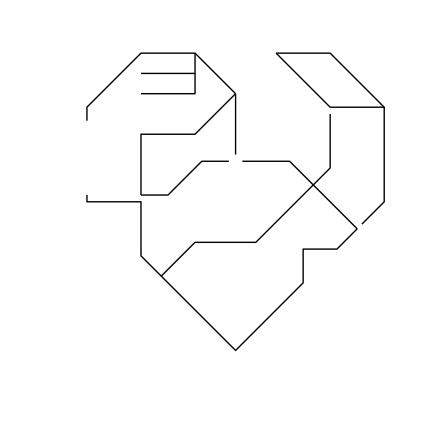

```mathematica
10/1.4
```

7.14286

```mathematica
Graphics[{Line[{#⟦All,1⟧,525-#⟦All,2⟧}ᵀ&/@data]}]
```

-Graphics-